# Gaussian/Normal Distributions

Christopher Lum
christopher.w.lum@gmail.com

This document accompanies the YouTube video at https://youtu.be/Xaju4l9KTE0.

Define the Gaussian/Normal distribution function

```mathematica
f[x_,μ_,σ_]=1/(σ (2 π)^(1/2))Exp[-1/2((x-μ)/σ)^2];
```

Plot this for various μ and σ values

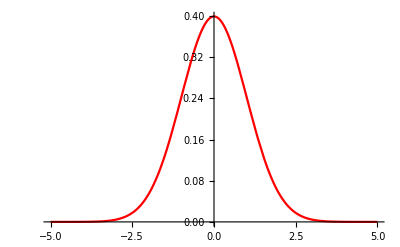

```mathematica
p1=Plot[f[x,0,1],{x,-5,5},PlotStyle->Red]
```

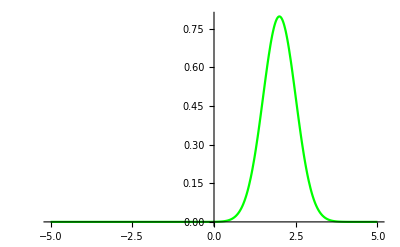

```mathematica
p2=Plot[f[x,2,1/2],{x,-5,5},PlotStyle->Green,PlotRange->All]
```

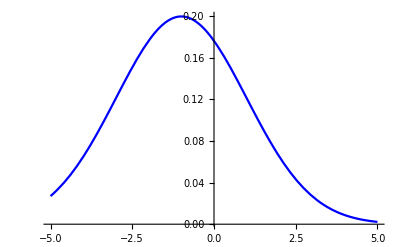

```mathematica
p3=Plot[f[x,-1,2],{x,-5,5},PlotStyle->Blue,PlotRange->All]
```

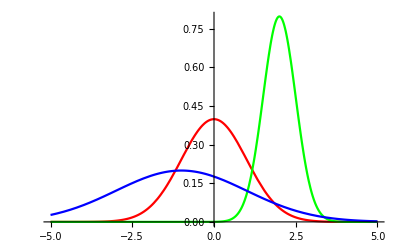

```mathematica
Show[p1,p2,p3,PlotRange->All]
```

Mathematica has the ‘NormalDistribution’ function to represent a Gaussian

```mathematica
NormalDistribution[μ,σ]
```

NormalDistribution[μ,σ]

By itself, this isn’t useful, but in conjunction with the ‘PDF’ function in Mathematica we can obtain the functional description

```mathematica
f2[x_,μ_,σ_]=PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
f[x,μ,σ]==f2[x,μ,σ]
```

True

Consider the normal/gaussian with μ=0 and σ=(1/2)^(1/2)

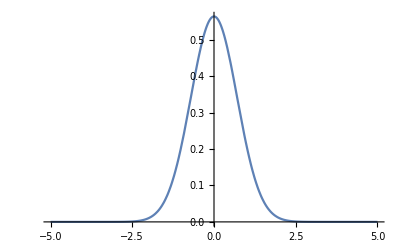

```mathematica
Plot[f[x,0,(1/2)^(1/2)],{x,-5,5}]
```

Compute probability that sample falls between [-x,x]

```mathematica
Integrate[f[t,0,(1/2)^(1/2)],{t,-x,x}]
```

Erf[x]

Plot the error function

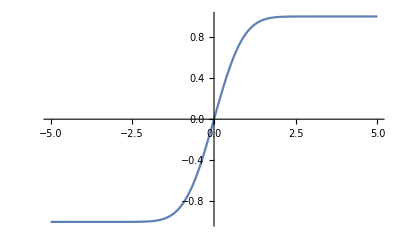

```mathematica
Plot[Erf[x],{x,-5,5}]
```

Compute the cumulative distribution function, F(x)

```mathematica
F[x_,μ_,σ_]=Simplify[Integrate[f[t,μ,σ],{t,-∞,x}],{σ>0}]
```

1/2 (1+Erf[(x-μ)/(√2 σ)])

Mathematica also has the ‘CDF’ function

```mathematica
F2[x_,μ_,σ_]=CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

Erfc is the ‘complimentary error function’

	erfc(x)=1-erf(x)

```mathematica
F[x,μ,σ]==F2[x,μ,σ]//FullSimplify
```

True

Plot F(x) for various μ and σ

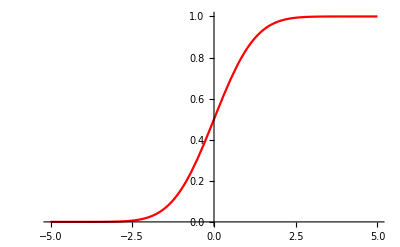

```mathematica
p1=Plot[F[x,0,1],{x,-5,5},PlotStyle->Red]
```

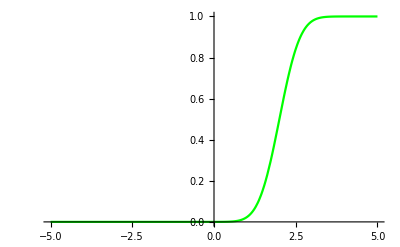

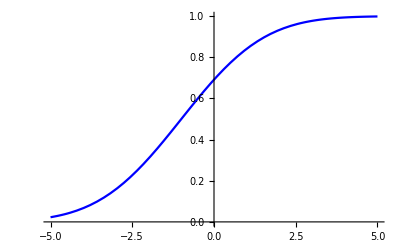

```mathematica
p2=Plot[F[x,2,1/2],{x,-5,5},PlotStyle->Green]
p3=Plot[F[x,-1,2],{x,-5,5},PlotStyle->Blue]
```

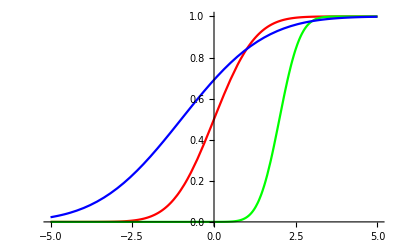

```mathematica
Show[p1,p2,p3,PlotRange->All]
```

Define the standard cumulative normal distribution

```mathematica
Φ[x_]=F[x,0,1]
```

1/2 (1+Erf[x/(√2)])

Prove theorem 1 (by direct substitution)

```mathematica
F[x,μ,σ]==Φ[(x-μ)/σ]
```

True

Double check our answers

```mathematica
F[2.44,0.8,2]
1/2(1+Erf[1/(2)^(1/2)((2.44-0.8)/2)])
```

0.793892

0.793892

```mathematica
1-F[1,0.8,2]
1-(1/2(1+Erf[1/(2)^(1/2)((1-0.8)/2)]))
```

0.460172

0.460172

```mathematica
F[1.8,0.8,2]-F[1,0.8,2]
1/2(1+Erf[1/(2)^(1/2)((1.8-0.8)/2)])-1/2(1+Erf[1/(2)^(1/2)((1-0.8)/2)])
```

0.151635

0.151635

Verify the 1, 2, 3 sigma limit

```mathematica
F[μ+3 σ,μ,σ]-F[μ-3 σ,μ,σ]//N
```

0.9973